```mathematica
Clear[c,ct,α,ω,p,s,ϕMC,KRC,γ]
```

```mathematica
c=α/4(√(1+(8ct)/α)-1)
```

1/4 (-1+√(1+(8 ct)/α)) α

```mathematica
α=√(1600/5.6)
ω=130.
p=25.
```

16.9031

130.

25.

```mathematica
s=0.02
```

0.02

```mathematica
Clear[r1]
```

```mathematica
ee=Table[{r1,NSolve[-ct/r1+s+((-1+√(1+(8 ct)/α))^2 α^2)/(16 (1+1/16 (1+1/p) (-1+√(1+(8 ct)/α))^2 α^2+((-1+√(1+(8 ct)/α))^4 α^4 ω)/(256 p)))==0,ct,Reals]},{r1,0.05,5,0.01}]
```

{{0.05,{{ct→0.00100005}}},{0.06,{{ct→0.00120009}}},{0.07,{{ct→0.00140014}}},{0.08,{{ct→0.0016002}}},{0.09,{{ct→0.00180029}}},{0.1,{{ct→0.0020004}}},{0.11,{{ct→0.00220053}}},{0.12,{{ct→0.00240069}}},{0.13,{{ct→0.00260088}}},{0.14,{{ct→0.0028011}}},{0.15,{{ct→0.00300135}}},{0.16,{{ct→0.00320164}}},{0.17,{{ct→0.00340197}}},{0.18,{{ct→0.00360233}}},{0.19,{{ct→0.00380275}}},{0.2,{{ct→0.0040032}}},{0.21,{{ct→0.00420371}}},{0.22,{{ct→0.00440426}}},{0.23,{{ct→0.00460487}}},{0.24,{{ct→0.00480554}}},{0.25,{{ct→0.00500626}}},{0.26,{{ct→0.00520704}}},{0.27,{{ct→0.00540789}}},{0.28,{{ct→0.0056088}}},{0.29,{{ct→0.00580977}}},{0.3,{{ct→0.00601082}}},{0.31,{{ct→0.00621194}}},{0.32,{{ct→0.00641314}}},{0.33,{{ct→0.00661441}}},{0.34,{{ct→0.00681577}}},{0.35,{{ct→0.0070172}}},{0.36,{{ct→0.00721873}}},{0.37,{{ct→0.00742034}}},{0.38,{{ct→0.00762204}}},{0.39,{{ct→0.00782383}}},{0.4,{{ct→0.00802571}}},{0.41,{{ct→0.0082277}}},{0.42,{{ct→0.00842978}}},{0.43,{{ct→0.00863197}}},{0.44,{{ct→0.00883427}}},{0.45,{{ct→0.00903667}}},{0.46,{{ct→0.00923918}}},{0.47,{{ct→0.0094418}}},{0.48,{{ct→0.00964454}}},{0.49,{{ct→0.0098474}}},{0.5,{{ct→0.0100504}}},{0.51,{{ct→0.0102535}}},{0.52,{{ct→0.0104567}}},{0.53,{{ct→0.0106601}}},{0.54,{{ct→0.0108636}}},{0.55,{{ct→0.0110672}}},{0.56,{{ct→0.0112709}}},{0.57,{{ct→0.0114748}}},{0.58,{{ct→0.0116789}}},{0.59,{{ct→0.0118831}}},{0.6,{{ct→0.0120874}}},{0.61,{{ct→0.0122919}}},{0.62,{{ct→0.0124965}}},{0.63,{{ct→0.0127013}}},{0.64,{{ct→0.0129063}}},{0.65,{{ct→0.0131114}}},{0.66,{{ct→0.0133167}}},{0.67,{{ct→0.0135221}}},{0.68,{{ct→0.0137277}}},{0.69,{{ct→0.0139335}}},{0.7,{{ct→0.0141395}}},{0.71,{{ct→0.0143456}}},{0.72,{{ct→0.0145519}}},{0.73,{{ct→0.0147584}}},{0.74,{{ct→0.0149651}}},{0.75,{{ct→0.015172}}},{0.76,{{ct→0.0153791}}},{0.77,{{ct→0.0155863}}},{0.78,{{ct→0.0157938}}},{0.79,{{ct→0.0160015}}},{0.8,{{ct→0.0162093}}},{0.81,{{ct→0.0164174}}},{0.82,{{ct→0.0166257}}},{0.83,{{ct→0.0168342}}},{0.84,{{ct→0.0170429}}},{0.85,{{ct→0.0172519}}},{0.86,{{ct→0.017461}}},{0.87,{{ct→0.0176704}}},{0.88,{{ct→0.0178801}}},{0.89,{{ct→0.0180899}}},{0.9,{{ct→0.0183}}},{0.91,{{ct→0.0185103}}},{0.92,{{ct→0.0187209}}},{0.93,{{ct→0.0189317}}},{0.94,{{ct→0.0191428}}},{0.95,{{ct→0.0193541}}},{0.96,{{ct→0.0195657}}},{0.97,{{ct→0.0197775}}},{0.98,{{ct→0.0199896}}},{0.99,{{ct→0.0202019}}},{1.,{{ct→0.0204146}}},{1.01,{{ct→0.0206275}}},{1.02,{{ct→0.0208406}}},{1.03,{{ct→0.0210541}}},{1.04,{{ct→0.0212678}}},{1.05,{{ct→0.0214819}}},{1.06,{{ct→0.0216962}}},{1.07,{{ct→0.0219108}}},{1.08,{{ct→0.0221257}}},{1.09,{{ct→0.0223409}}},{1.1,{{ct→0.0225564}}},{1.11,{{ct→0.0227722}}},{1.12,{{ct→0.0229884}}},{1.13,{{ct→0.0232048}}},{1.14,{{ct→0.0234216}}},{1.15,{{ct→0.0236387}}},{1.16,{{ct→0.0238561}}},{1.17,{{ct→0.0240738}}},{1.18,{{ct→0.0242919}}},{1.19,{{ct→0.0245103}}},{1.2,{{ct→0.0247291}}},{1.21,{{ct→0.0249482}}},{1.22,{{ct→0.0251677}}},{1.23,{{ct→0.0253875}}},{1.24,{{ct→0.0256077}}},{1.25,{{ct→0.0258282}}},{1.26,{{ct→0.0260492}}},{1.27,{{ct→0.0262704}}},{1.28,{{ct→0.0264921}}},{1.29,{{ct→0.0267142}}},{1.3,{{ct→0.0269366}}},{1.31,{{ct→0.0271594}}},{1.32,{{ct→0.0273826}}},{1.33,{{ct→0.0276062}}},{1.34,{{ct→0.0278303}}},{1.35,{{ct→0.0280547}}},{1.36,{{ct→0.0282795}}},{1.37,{{ct→0.0285048}}},{1.38,{{ct→0.0287305}}},{1.39,{{ct→0.0289566}}},{1.4,{{ct→0.0291831}}},{1.41,{{ct→0.0294101}}},{1.42,{{ct→0.0296375}}},{1.43,{{ct→0.0298654}}},{1.44,{{ct→0.0300937}}},{1.45,{{ct→0.0303225}}},{1.46,{{ct→0.0305517}}},{1.47,{{ct→0.0307814}}},{1.48,{{ct→0.0310116}}},{1.49,{{ct→0.0312422}}},{1.5,{{ct→0.0314734}}},{1.51,{{ct→0.031705}}},{1.52,{{ct→0.0319371}}},{1.53,{{ct→0.0321698}}},{1.54,{{ct→0.0324029}}},{1.55,{{ct→0.0326365}}},{1.56,{{ct→0.0328707}}},{1.57,{{ct→0.0331054}}},{1.58,{{ct→0.0333406}}},{1.59,{{ct→0.0335763}}},{1.6,{{ct→0.0338126}}},{1.61,{{ct→0.0340495}}},{1.62,{{ct→0.0342869}}},{1.63,{{ct→0.0345248}}},{1.64,{{ct→0.0347633}}},{1.65,{{ct→0.0350024}}},{1.66,{{ct→0.0352421}}},{1.67,{{ct→0.0354823}}},{1.68,{{ct→0.0357232}}},{1.69,{{ct→0.0359646}}},{1.7,{{ct→0.0362067}}},{1.71,{{ct→0.0364493}}},{1.72,{{ct→0.0366926}}},{1.73,{{ct→0.0369365}}},{1.74,{{ct→0.0371811}}},{1.75,{{ct→0.0374263}}},{1.76,{{ct→0.0376721}}},{1.77,{{ct→0.0379186}}},{1.78,{{ct→0.0381658}}},{1.79,{{ct→0.0384136}}},{1.8,{{ct→0.0386621}}},{1.81,{{ct→0.0389113}}},{1.82,{{ct→0.0391612}}},{1.83,{{ct→0.0394118}}},{1.84,{{ct→0.0396631}}},{1.85,{{ct→0.0399151}}},{1.86,{{ct→0.0401679}}},{1.87,{{ct→0.0404214}}},{1.88,{{ct→0.0406756}}},{1.89,{{ct→0.0409306}}},{1.9,{{ct→0.0411864}}},{1.91,{{ct→0.0414429}}},{1.92,{{ct→0.0417002}}},{1.93,{{ct→0.0419583}}},{1.94,{{ct→0.0422172}}},{1.95,{{ct→0.0424769}}},{1.96,{{ct→0.0427375}}},{1.97,{{ct→0.0429988}}},{1.98,{{ct→0.043261}}},{1.99,{{ct→0.0435241}}},{2.,{{ct→0.043788}}},{2.01,{{ct→0.0440528}}},{2.02,{{ct→0.0443185}}},{2.03,{{ct→0.044585}}},{2.04,{{ct→0.0448525}}},{2.05,{{ct→0.0451209}}},{2.06,{{ct→0.0453902}}},{2.07,{{ct→0.0456604}}},{2.08,{{ct→0.0459317}}},{2.09,{{ct→0.0462038}}},{2.1,{{ct→0.046477}}},{2.11,{{ct→0.0467511}}},{2.12,{{ct→0.0470262}}},{2.13,{{ct→0.0473023}}},{2.14,{{ct→0.0475795}}},{2.15,{{ct→0.0478577}}},{2.16,{{ct→0.048137}}},{2.17,{{ct→0.0484173}}},{2.18,{{ct→0.0486987}}},{2.19,{{ct→0.0489812}}},{2.2,{{ct→0.0492648}}},{2.21,{{ct→0.0495495}}},{2.22,{{ct→0.0498354}}},{2.23,{{ct→0.0501224}}},{2.24,{{ct→0.0504106}}},{2.25,{{ct→0.0507}}},{2.26,{{ct→0.0509906}}},{2.27,{{ct→0.0512824}}},{2.28,{{ct→0.0515754}}},{2.29,{{ct→0.0518697}}},{2.3,{{ct→0.0521652}}},{2.31,{{ct→0.0524621}}},{2.32,{{ct→0.0527602}}},{2.33,{{ct→0.0530597}}},{2.34,{{ct→0.0533605}}},{2.35,{{ct→0.0536627}}},{2.36,{{ct→0.0539662}}},{2.37,{{ct→0.0542712}}},{2.38,{{ct→0.0545776}}},{2.39,{{ct→0.0548854}}},{2.4,{{ct→0.0551947}}},{2.41,{{ct→0.0555055}}},{2.42,{{ct→0.0558177}}},{2.43,{{ct→0.0561315}}},{2.44,{{ct→0.0564469}}},{2.45,{{ct→0.0567639}}},{2.46,{{ct→0.0570824}}},{2.47,{{ct→0.0574026}}},{2.48,{{ct→0.0577244}}},{2.49,{{ct→0.0580479}}},{2.5,{{ct→0.0583731}}},{2.51,{{ct→0.0587}}},{2.52,{{ct→0.0590287}}},{2.53,{{ct→0.0593592}}},{2.54,{{ct→0.0596915}}},{2.55,{{ct→0.0600257}}},{2.56,{{ct→0.0603617}}},{2.57,{{ct→0.0606996}}},{2.58,{{ct→0.0610395}}},{2.59,{{ct→0.0613813}}},{2.6,{{ct→0.0617252}}},{2.61,{{ct→0.0620711}}},{2.62,{{ct→0.0624191}}},{2.63,{{ct→0.0627691}}},{2.64,{{ct→0.0631214}}},{2.65,{{ct→0.0634758}}},{2.66,{{ct→0.0638324}}},{2.67,{{ct→0.0641913}}},{2.68,{{ct→0.0645525}}},{2.69,{{ct→0.0649161}}},{2.7,{{ct→0.065282}}},{2.71,{{ct→0.0656504}}},{2.72,{{ct→0.0660213}}},{2.73,{{ct→0.0663947}}},{2.74,{{ct→0.0667707}}},{2.75,{{ct→0.0671493}}},{2.76,{{ct→0.0675306}}},{2.77,{{ct→0.0679146}}},{2.78,{{ct→0.0683014}}},{2.79,{{ct→0.0686911}}},{2.8,{{ct→0.0690836}}},{2.81,{{ct→0.0694792}}},{2.82,{{ct→0.0698777}}},{2.83,{{ct→0.0702794}}},{2.84,{{ct→0.0706841}}},{2.85,{{ct→0.0710922}}},{2.86,{{ct→0.0715035}}},{2.87,{{ct→0.0719181}}},{2.88,{{ct→0.0723362}}},{2.89,{{ct→0.0727579}}},{2.9,{{ct→0.0731831}}},{2.91,{{ct→0.073612}}},{2.92,{{ct→0.0740447},{ct→0.431934},{ct→0.47014}}},{2.93,{{ct→0.0744812},{ct→0.414932},{ct→0.487433}}},{2.94,{{ct→0.0749217},{ct→0.403749},{ct→0.498903}}},{2.95,{{ct→0.0753662},{ct→0.394781},{ct→0.508154}}},{2.96,{{ct→0.0758149},{ct→0.387081},{ct→0.516133}}},{2.97,{{ct→0.0762678},{ct→0.380231},{ct→0.523258}}},{2.98,{{ct→0.076725},{ct→0.373999},{ct→0.52976}}},{2.99,{{ct→0.0771868},{ct→0.368245},{ct→0.53578}}},{3.,{{ct→0.0776531},{ct→0.362872},{ct→0.541414}}},{3.01,{{ct→0.0781241},{ct→0.357814},{ct→0.546728}}},{3.02,{{ct→0.0786},{ct→0.353021},{ct→0.551773}}},{3.03,{{ct→0.0790808},{ct→0.348454},{ct→0.556587}}},{3.04,{{ct→0.0795667},{ct→0.344083},{ct→0.561199}}},{3.05,{{ct→0.0800578},{ct→0.339885},{ct→0.565633}}},{3.06,{{ct→0.0805544},{ct→0.33584},{ct→0.569909}}},{3.07,{{ct→0.0810564},{ct→0.33193},{ct→0.574044}}},{3.08,{{ct→0.0815642},{ct→0.328144},{ct→0.57805}}},{3.09,{{ct→0.0820779},{ct→0.324468},{ct→0.581939}}},{3.1,{{ct→0.0825976},{ct→0.320893},{ct→0.585721}}},{3.11,{{ct→0.0831236},{ct→0.31741},{ct→0.589405}}},{3.12,{{ct→0.083656},{ct→0.314011},{ct→0.592998}}},{3.13,{{ct→0.0841951},{ct→0.31069},{ct→0.596507}}},{3.14,{{ct→0.084741},{ct→0.307441},{ct→0.599937}}},{3.15,{{ct→0.085294},{ct→0.304257},{ct→0.603294}}},{3.16,{{ct→0.0858544},{ct→0.301135},{ct→0.606582}}},{3.17,{{ct→0.0864223},{ct→0.298069},{ct→0.609806}}},{3.18,{{ct→0.0869981},{ct→0.295057},{ct→0.612969}}},{3.19,{{ct→0.087582},{ct→0.292093},{ct→0.616075}}},{3.2,{{ct→0.0881743},{ct→0.289175},{ct→0.619126}}},{3.21,{{ct→0.0887754},{ct→0.2863},{ct→0.622126}}},{3.22,{{ct→0.0893856},{ct→0.283464},{ct→0.625077}}},{3.23,{{ct→0.0900052},{ct→0.280666},{ct→0.627982}}},{3.24,{{ct→0.0906347},{ct→0.277901},{ct→0.630843}}},{3.25,{{ct→0.0912743},{ct→0.275169},{ct→0.633661}}},{3.26,{{ct→0.0919246},{ct→0.272466},{ct→0.636438}}},{3.27,{{ct→0.092586},{ct→0.269791},{ct→0.639177}}},{3.28,{{ct→0.093259},{ct→0.267141},{ct→0.641879}}},{3.29,{{ct→0.0939442},{ct→0.264514},{ct→0.644546}}},{3.3,{{ct→0.094642},{ct→0.261909},{ct→0.647178}}},{3.31,{{ct→0.0953531},{ct→0.259323},{ct→0.649778}}},{3.32,{{ct→0.0960782},{ct→0.256754},{ct→0.652346}}},{3.33,{{ct→0.0968179},{ct→0.254201},{ct→0.654883}}},{3.34,{{ct→0.0975731},{ct→0.251662},{ct→0.657391}}},{3.35,{{ct→0.0983445},{ct→0.249135},{ct→0.659871}}},{3.36,{{ct→0.0991331},{ct→0.246618},{ct→0.662323}}},{3.37,{{ct→0.0999398},{ct→0.244109},{ct→0.664749}}},{3.38,{{ct→0.100766},{ct→0.241606},{ct→0.66715}}},{3.39,{{ct→0.101612},{ct→0.239107},{ct→0.669525}}},{3.4,{{ct→0.10248},{ct→0.236611},{ct→0.671877}}},{3.41,{{ct→0.103372},{ct→0.234114},{ct→0.674205}}},{3.42,{{ct→0.104288},{ct→0.231615},{ct→0.67651}}},{3.43,{{ct→0.105231},{ct→0.229111},{ct→0.678794}}},{3.44,{{ct→0.106203},{ct→0.2266},{ct→0.681057}}},{3.45,{{ct→0.107205},{ct→0.224078},{ct→0.683298}}},{3.46,{{ct→0.108241},{ct→0.221542},{ct→0.68552}}},{3.47,{{ct→0.109314},{ct→0.218989},{ct→0.687722}}},{3.48,{{ct→0.110427},{ct→0.216415},{ct→0.689905}}},{3.49,{{ct→0.111583},{ct→0.213816},{ct→0.692069}}},{3.5,{{ct→0.112789},{ct→0.211185},{ct→0.694216}}},{3.51,{{ct→0.114048},{ct→0.208518},{ct→0.696344}}},{3.52,{{ct→0.115368},{ct→0.205808},{ct→0.698456}}},{3.53,{{ct→0.116757},{ct→0.203045},{ct→0.70055}}},{3.54,{{ct→0.118225},{ct→0.200219},{ct→0.702629}}},{3.55,{{ct→0.119784},{ct→0.197318},{ct→0.704691}}},{3.56,{{ct→0.121451},{ct→0.194325},{ct→0.706738}}},{3.57,{{ct→0.123246},{ct→0.191218},{ct→0.708769}}},{3.58,{{ct→0.125198},{ct→0.187969},{ct→0.710786}}},{3.59,{{ct→0.127351},{ct→0.184534},{ct→0.712788}}},{3.6,{{ct→0.129767},{ct→0.180849},{ct→0.714776}}},{3.61,{{ct→0.132555},{ct→0.176807},{ct→0.71675}}},{3.62,{{ct→0.135919},{ct→0.172201},{ct→0.71871}}},{3.63,{{ct→0.140374},{ct→0.166518},{ct→0.720657}}},{3.64,{{ct→0.148984},{ct→0.156693},{ct→0.72259}}},{3.65,{{ct→0.724511}}},{3.66,{{ct→0.726419}}},{3.67,{{ct→0.728315}}},{3.68,{{ct→0.730199}}},{3.69,{{ct→0.732071}}},{3.7,{{ct→0.733932}}},{3.71,{{ct→0.735781}}},{3.72,{{ct→0.737619}}},{3.73,{{ct→0.739445}}},{3.74,{{ct→0.741261}}},{3.75,{{ct→0.743067}}},{3.76,{{ct→0.744862}}},{3.77,{{ct→0.746647}}},{3.78,{{ct→0.748422}}},{3.79,{{ct→0.750186}}},{3.8,{{ct→0.751942}}},{3.81,{{ct→0.753687}}},{3.82,{{ct→0.755424}}},{3.83,{{ct→0.75715}}},{3.84,{{ct→0.758868}}},{3.85,{{ct→0.760577}}},{3.86,{{ct→0.762277}}},{3.87,{{ct→0.763969}}},{3.88,{{ct→0.765652}}},{3.89,{{ct→0.767326}}},{3.9,{{ct→0.768993}}},{3.91,{{ct→0.770651}}},{3.92,{{ct→0.772301}}},{3.93,{{ct→0.773943}}},{3.94,{{ct→0.775577}}},{3.95,{{ct→0.777204}}},{3.96,{{ct→0.778823}}},{3.97,{{ct→0.780435}}},{3.98,{{ct→0.782039}}},{3.99,{{ct→0.783636}}},{4.,{{ct→0.785226}}},{4.01,{{ct→0.786808}}},{4.02,{{ct→0.788384}}},{4.03,{{ct→0.789953}}},{4.04,{{ct→0.791515}}},{4.05,{{ct→0.79307}}},{4.06,{{ct→0.794619}}},{4.07,{{ct→0.796161}}},{4.08,{{ct→0.797697}}},{4.09,{{ct→0.799227}}},{4.1,{{ct→0.80075}}},{4.11,{{ct→0.802267}}},{4.12,{{ct→0.803777}}},{4.13,{{ct→0.805282}}},{4.14,{{ct→0.806781}}},{4.15,{{ct→0.808274}}},{4.16,{{ct→0.809761}}},{4.17,{{ct→0.811242}}},{4.18,{{ct→0.812717}}},{4.19,{{ct→0.814187}}},{4.2,{{ct→0.815652}}},{4.21,{{ct→0.81711}}},{4.22,{{ct→0.818564}}},{4.23,{{ct→0.820012}}},{4.24,{{ct→0.821454}}},{4.25,{{ct→0.822892}}},{4.26,{{ct→0.824324}}},{4.27,{{ct→0.825751}}},{4.28,{{ct→0.827173}}},{4.29,{{ct→0.82859}}},{4.3,{{ct→0.830002}}},{4.31,{{ct→0.831409}}},{4.32,{{ct→0.832811}}},{4.33,{{ct→0.834208}}},{4.34,{{ct→0.8356}}},{4.35,{{ct→0.836988}}},{4.36,{{ct→0.838371}}},{4.37,{{ct→0.83975}}},{4.38,{{ct→0.841123}}},{4.39,{{ct→0.842493}}},{4.4,{{ct→0.843858}}},{4.41,{{ct→0.845218}}},{4.42,{{ct→0.846574}}},{4.43,{{ct→0.847925}}},{4.44,{{ct→0.849273}}},{4.45,{{ct→0.850616}}},{4.46,{{ct→0.851954}}},{4.47,{{ct→0.853289}}},{4.48,{{ct→0.854619}}},{4.49,{{ct→0.855946}}},{4.5,{{ct→0.857268}}},{4.51,{{ct→0.858586}}},{4.52,{{ct→0.8599}}},{4.53,{{ct→0.86121}}},{4.54,{{ct→0.862517}}},{4.55,{{ct→0.863819}}},{4.56,{{ct→0.865117}}},{4.57,{{ct→0.866412}}},{4.58,{{ct→0.867703}}},{4.59,{{ct→0.86899}}},{4.6,{{ct→0.870273}}},{4.61,{{ct→0.871553}}},{4.62,{{ct→0.872829}}},{4.63,{{ct→0.874101}}},{4.64,{{ct→0.87537}}},{4.65,{{ct→0.876635}}},{4.66,{{ct→0.877897}}},{4.67,{{ct→0.879155}}},{4.68,{{ct→0.88041}}},{4.69,{{ct→0.881661}}},{4.7,{{ct→0.882909}}},{4.71,{{ct→0.884153}}},{4.72,{{ct→0.885394}}},{4.73,{{ct→0.886632}}},{4.74,{{ct→0.887866}}},{4.75,{{ct→0.889098}}},{4.76,{{ct→0.890325}}},{4.77,{{ct→0.89155}}},{4.78,{{ct→0.892772}}},{4.79,{{ct→0.89399}}},{4.8,{{ct→0.895205}}},{4.81,{{ct→0.896417}}},{4.82,{{ct→0.897626}}},{4.83,{{ct→0.898831}}},{4.84,{{ct→0.900034}}},{4.85,{{ct→0.901234}}},{4.86,{{ct→0.90243}}},{4.87,{{ct→0.903624}}},{4.88,{{ct→0.904815}}},{4.89,{{ct→0.906003}}},{4.9,{{ct→0.907187}}},{4.91,{{ct→0.908369}}},{4.92,{{ct→0.909548}}},{4.93,{{ct→0.910725}}},{4.94,{{ct→0.911898}}},{4.95,{{ct→0.913069}}},{4.96,{{ct→0.914236}}},{4.97,{{ct→0.915401}}},{4.98,{{ct→0.916563}}},{4.99,{{ct→0.917723}}},{5.,{{ct→0.91888}}}}

```mathematica
ее1Down={{0.05,0.001000049993117016},{0.060000000000000005,0.0012000863877791737},{0.07,0.001400137181160265},{0.08,0.0016002047743441372},{0.09,0.0018002915692902045},{0.1,0.002000399969023684},{0.11,0.0022005323778260142},{0.12000000000000001,0.002400691201425488},{0.13,0.0026008788471881474},{0.14,0.0028010977243089746},{0.15000000000000002,0.0030013502440034193},{0.16,0.0032016388196993077},{0.16999999999999998,0.003401965867229162},{0.18,0.003602333805022984},{0.19,0.003802745054301533},{0.2,0.004003202039270142},{0.21000000000000002,0.004203707187313112},{0.22000000000000003,0.004404262929188732},{0.22999999999999998,0.0046048716992249505},{0.24,0.0048055359355157565},{0.25,0.005006258080118303},{0.26,0.005207040579250816},{0.27,0.005407885883491329},{0.28,0.005608796447977297},{0.29,0.005809774732606111},{0.3,0.006010823202236587},{0.31,0.006211944326891436},{0.32,0.006413140581960798},{0.33,0.006614414448406849},{0.33999999999999997,0.006815768412969554},{0.35,0.007017204968373599},{0.36,0.007218726613536536},{0.37,0.007420335853778215},{0.38,0.00762203520103153},{0.39,0.007823827174054526},{0.4,0.008025714298643924},{0.41,0.008227699107850112},{0.42,0.00842978414219364},{0.43,0.00863197194988328},{0.44,0.008834265087035702},{0.45,0.009036666117896807},{0.46,0.009239177615064775},{0.47,0.009441802159714878},{0.48,0.009644542341826124},{0.49,0.009847400760409757},{0.5,0.010050380023739706},{0.51,0.010253482749584994},{0.52,0.010456711565444218},{0.53,0.010660069108782092},{0.54,0.010863558027268173},{0.55,0.01106718097901779},{0.56,0.011270940632835248},{0.5700000000000001,0.01147483966845937},{0.5800000000000001,0.011678880776811437},{0.5900000000000001,0.01188306666024558},{0.6000000000000001,0.012087400032801711},{0.6100000000000001,0.012291883620461035},{0.6200000000000001,0.012496520161404217},{0.63,0.01270131240627227},{0.64,0.01290626311843025},{0.65,0.013111375074233792},{0.66,0.013316651063298598},{0.67,0.013522093888772914},{0.68,0.013727706367613099},{0.6900000000000001,0.013933491330862347},{0.7000000000000001,0.014139451623932634},{0.7100000000000001,0.014345590106889973},{0.7200000000000001,0.014551909654743076},{0.7300000000000001,0.01475841315773546},{0.7400000000000001,0.014965103521641133},{0.7500000000000001,0.015171983668063892},{0.76,0.015379056534740369},{0.77,0.015586325075846867},{0.78,0.015793792262310116},{0.79,0.016001461082122012},{0.8,0.016209334540658444},{0.81,0.016417415661002306},{0.8200000000000001,0.01662570748427079},{0.8300000000000001,0.016834213069947045},{0.8400000000000001,0.01704293549621634},{0.8500000000000001,0.0172518778603068},{0.8600000000000001,0.017461043278834815},{0.8700000000000001,0.017670434888155298},{0.8800000000000001,0.017880055844716785},{0.89,0.018089909325421635},{0.9,0.018299998527991305},{0.91,0.01851032667133692},{0.92,0.018720896995935217},{0.93,0.018931712764209983},{0.9400000000000001,0.01914277726091913},{0.9500000000000001,0.01935409379354754},{0.9600000000000001,0.01956566569270579},{0.9700000000000001,0.019777496312534906},{0.9800000000000001,0.019989589031117302},{0.9900000000000001,0.020201947250894005},{1.,0.020414574399088364},{1.01,0.020627473928136346},{1.02,0.020840649316123595},{1.03,0.021054104067229424},{1.04,0.021267841712177847},{1.05,0.021481865808695898},{1.06,0.02169617994197931},{1.07,0.02191078772516583},{1.08,0.022125692799816243},{1.09,0.022340898836403365},{1.1,0.022556409534809158},{1.11,0.02277222862483016},{1.12,0.022988359866691413},{1.1300000000000001,0.02320480705156915},{1.1400000000000001,0.023421574002122334},{1.1500000000000001,0.02363866457303338},{1.1600000000000001,0.02385608265155821},{1.1700000000000002,0.024073832158085853},{1.1800000000000002,0.02429191704670788},{1.1900000000000002,0.02451034130579784},{1.2000000000000002,0.02472910895860097},{1.21,0.02494822406383444},{1.22,0.025167690716298347},{1.23,0.02538751304749776},{1.24,0.025607695226276032},{1.25,0.025828241459459726},{1.26,0.026049155992515345},{1.27,0.026270443110218245},{1.28,0.02649210713733398},{1.29,0.02671415243931236},{1.3,0.02693658342299462},{1.31,0.02715940453733394},{1.32,0.02738262027412967},{1.33,0.027606235168775653},{1.34,0.027830253801022914},{1.35,0.02805468079575713},{1.36,0.02827952082379125},{1.37,0.028504778602673638},{1.3800000000000001,0.0287304588975121},{1.3900000000000001,0.028956566521814272},{1.4000000000000001,0.029183106338344714},{1.4100000000000001,0.02941008325999919},{1.4200000000000002,0.02963750225069653},{1.4300000000000002,0.029865368326288572},{1.4400000000000002,0.030093686555488625},{1.4500000000000002,0.030322462060818938},{1.46,0.03055170001957767},{1.47,0.030781405664825904},{1.48,0.031011584286395156},{1.49,0.03124224123191602},{1.5,0.031473381907868435},{1.51,0.03170501178065415},{1.52,0.03193713637769208},{1.53,0.03216976128853698},{1.54,0.0324028921660223},{1.55,0.03263653472742766},{1.56,0.03287069475567177},{1.57,0.03310537810053137},{1.58,0.033340590679887046},{1.59,0.03357633848099649},{1.6,0.033812627561796135},{1.61,0.03404946405223182},{1.62,0.03428685415561937},{1.6300000000000001,0.03452480415003592},{1.6400000000000001,0.03476332038974282},{1.6500000000000001,0.035002409306641065},{1.6600000000000001,0.0352420774117601},{1.6700000000000002,0.035482331296781064},{1.6800000000000002,0.03572317763559536},{1.6900000000000002,0.03596462318589962},{1.7000000000000002,0.03620667479082813},{1.7100000000000002,0.03644933938062374},{1.72,0.0366926239743485},{1.73,0.0369365356816351},{1.74,0.03718108170448035},{1.75,0.03742626933908193},{1.76,0.03767210597771974},{1.77,0.037918599110683224},{1.78,0.038165756328245884},{1.79,0.038413585322688654},{1.8,0.03866209389037345},{1.81,0.038911289933868484},{1.82,0.039161181464127004},{1.83,0.03941177660272096},{1.84,0.03966308358413151},{1.85,0.03991511075809795},{1.86,0.04016786659202707},{1.87,0.040421359673464725},{1.8800000000000001,0.04067559871263169},{1.8900000000000001,0.040930592545025776},{1.9000000000000001,0.04118635013409242},{1.9100000000000001,0.04144288057396596},{1.9200000000000002,0.04170019309228375},{1.9300000000000002,0.04195829705307574},{1.9400000000000002,0.04221720195973182},{1.9500000000000002,0.04247691745804956},{1.9600000000000002,0.04273745333936502},{1.97,0.04299881954376944},{1.98,0.043261026163414686},{1.99,0.04352408344591038},{2.,0.04378800179781603},{2.01,0.04405279178823116},{2.02,0.0443184641524871},{2.03,0.044585029795943726},{2.04,0.04485249979789493},{2.05,0.04512088541558664},{2.06,0.04539019808835136},{2.07,0.0456604494418633},{2.08,0.04593165129251856},{2.09,0.046203815651944695},{2.0999999999999996,0.04647695473164453},{2.11,0.046751080947778946},{2.1199999999999997,0.04702620692609389},{2.13,0.047302345506996815},{2.1399999999999997,0.04757950975078822},{2.15,0.04785771294305396},{2.1599999999999997,0.048136968600224525},{2.17,0.048417290475307524},{2.1799999999999997,0.04869869256380001},{2.19,0.04898118910978757},{2.1999999999999997,0.04926479461223743},{2.21,0.04954952383149302},{2.2199999999999998,0.049835391795978116},{2.23,0.050122413809118575},{2.2399999999999998,0.050410605456490565},{2.25,0.050699982613204166},{2.26,0.050990561451531975},{2.27,0.0512823584487926},{2.28,0.051575390395499486},{2.29,0.05186967440378604},{2.3,0.052165227916118447},{2.31,0.052462068714308356},{2.32,0.05276021492883793},{2.33,0.053059685048510545},{2.34,0.05336049793044117},{2.35,0.05366267281040097},{2.36,0.053966229313531525},{2.3699999999999997,0.05427118746544487},{2.38,0.054577567703726404},{2.3899999999999997,0.05488539088985848},{2.4,0.055194678321583604},{2.4099999999999997,0.0555054517457271},{2.42,0.05581773337150012},{2.4299999999999997,0.05613154588430501},{2.44,0.056446912460066445},{2.4499999999999997,0.056763856780112615},{2.46,0.05708240304663252},{2.4699999999999998,0.05740257599873669},{2.48,0.05772440092915005},{2.4899999999999998,0.058047903701567635},{2.5,0.05837311076870525},{2.51,0.058700049191079205},{2.52,0.059028746656551376},{2.53,0.05935923150067756},{2.54,0.05969153272789987},{2.55,0.06002568003362592},{2.56,0.060361703827240334},{2.57,0.06069963525609696},{2.58,0.06103950623054286},{2.59,0.06138134945002873},{2.6,0.061725198430363386},{2.61,0.06207108753217396},{2.6199999999999997,0.062419051990637235},{2.63,0.06276912794655168},{2.6399999999999997,0.06312135247882451},{2.65,0.06347576363845284},{2.6599999999999997,0.06383240048408304},{2.67,0.0641913031192388},{2.6799999999999997,0.06455251273131342},{2.69,0.0649160716324294},{2.6999999999999997,0.06528202330227514},{2.71,0.06565041243303595},{2.7199999999999998,0.06602128497654546},{2.73,0.06639468819379216},{2.7399999999999998,0.06677067070692555},{2.75,0.06714928255391694},{2.76,0.06753057524604167},{2.77,0.06791460182836162},{2.78,0.06830141694340049},{2.79,0.06869107689821932},{2.8,0.06908363973511539},{2.81,0.06947916530618523},{2.82,0.06987771535201177},{2.83,0.07027935358475625},{2.84,0.07068414577595815},{2.85,0.07109215984937188},{2.86,0.07150346597919566},{2.8699999999999997,0.07191813669407845},{2.88,0.07233624698732351},{2.8899999999999997,0.07275787443374332},{2.9,0.07318309931366071},{2.9099999999999997,0.07361200474459466},{2.92,0.07404467682121788},{2.9299999999999997,0.07448120476422682},{2.94,0.07492168107882423},{2.9499999999999997,0.0753662017235796},{2.96,0.07581486629050631},{2.9699999999999998,0.07626777819727494},{2.98,0.07672504489257248},{2.9899999999999998,0.07718677807571765},{3.,0.07765309393175478},{3.01,0.0781241133833741},{3.02,0.07859996236114691},{3.03,0.07908077209372157},{3.04,0.07956667941980375},{3.05,0.0800578271239438},{3.06,0.08055436429837907},{3.07,0.08105644673343411},{3.08,0.08156423733926917},{3.09,0.08207790660209548},{3.1,0.08259763307834748},{3.11,0.08312360393072678},{3.12,0.08365601551051756},{3.13,0.08419507399112895},{3.1399999999999997,0.08474099605845707},{3.15,0.08529400966439483},{3.1599999999999997,0.0858543548506646},{3.17,0.0864222846511307},{3.1799999999999997,0.08699806608188793},{3.19,0.08758198122974888},{3.1999999999999997,0.08817432845130303},{3.21,0.08877542369653636},{3.2199999999999998,0.08938560197313608},{3.23,0.09000521897012594},{3.2399999999999998,0.09063465286246265},{3.25,0.09127430632177468},{3.26,0.09192460876266334},{3.27,0.0925860188590701},{3.28,0.0932590273713362},{3.29,0.09394416033199139},{3.3,0.09464198264732078},{3.31,0.09535310218277802},{3.32,0.0960781744138601},{3.33,0.09681790774081026},{3.34,0.0975730695863604},{3.35,0.09834449342182958},{3.36,0.09913308689981948},{3.37,0.09993984131358123},{3.38,0.10076584265670059},{3.3899999999999997,0.1016122846259394},{3.4,0.10248048400024404},{3.4099999999999997,0.10337189894759774},{3.42,0.10428815096919893},{3.4299999999999997,0.10523105140268894},{3.44,0.10620263369512592},{3.4499999999999997,0.10720519305512377},{3.46,0.10824133565178946},{3.4699999999999998,0.10931404032214688},{3.48,0.11042673689826964},{3.4899999999999998,0.11158340696212851},{3.5,0.1127887153954295},{3.51,0.11404818504645715},{3.52,0.1153684331162052},{3.53,0.11675749815398108},{3.54,0.11822530401754044},{3.55,0.11978433805511231},{3.56,0.12145067817607665},{3.57,0.12324561653165612},{3.58,0.12519836657120664},{3.59,0.1273508927425114},{3.6,0.12976733529060683},{3.61,0.13255485285261268},{3.62,0.1359193492745732},{3.63,0.14037421760891805},{3.6399999999999997,0.14898362747632463}};
```

```mathematica
ее1Middle={{2.92,0.4319339869006405},{2.9299999999999997,0.41493243691993714},{2.94,0.40374947753454776},{2.9499999999999997,0.39478113835936074},{2.96,0.38708127894274647},{2.9699999999999998,0.3802305025625113},{2.98,0.37399901515225803},{2.9899999999999998,0.368244681521413},{3.,0.36287229838093105},{3.01,0.35781437943251293},{3.02,0.35302100706812595},{3.03,0.34845401286801225},{3.04,0.3440834235434024},{3.05,0.33988517942320295},{3.06,0.3358396092275126},{3.07,0.33193037551451876},{3.08,0.3281437245252136},{3.09,0.3244679394042062},{3.1,0.32089293315108663},{3.11,0.31740993993014766},{3.12,0.3140112771015828},{3.13,0.31069015906436104},{3.1399999999999997,0.30744054969387413},{3.15,0.3042570439588887},{3.1599999999999997,0.3011347718943226},{3.17,0.29806931990716523},{3.1799999999999997,0.2950566656653316},{3.19,0.29209312373225144},{3.1999999999999997,0.28917529977422773},{3.21,0.28630005165691613},{3.2199999999999998,0.28346445611180404},{3.23,0.2806657799278266},{3.2399999999999998,0.2779014548313475},{3.25,0.27516905537669983},{3.26,0.27246627929147643},{3.27,0.26979092981455205},{3.28,0.26714089963673926},{3.29,0.2645141561086233},{3.3,0.2619087274207835},{3.31,0.259322689490616},{3.32,0.2567541533088691},{3.33,0.2542012525087065},{3.34,0.25166213092095113},{3.35,0.24913492987092492},{3.36,0.2466177749541713},{3.37,0.24410876199881984},{3.38,0.24160594187906256},{3.3899999999999997,0.23910730378365153},{3.4,0.23661075646042146},{3.4099999999999997,0.2341141068453248},{3.42,0.2316150353318792},{3.4299999999999997,0.22911106672913106},{3.44,0.22659953567106605},{3.4499999999999997,0.22407754484493136},{3.46,0.22154191385052355},{3.4699999999999998,0.21898911571085777},{3.48,0.21641519690719097},{3.4899999999999998,0.21381567511640268},{3.5,0.21118540627104587},{3.51,0.2085184086090159},{3.52,0.20580762510072326},{3.53,0.20304459535480437},{3.54,0.20021899063946139},{3.55,0.19731793475503231},{3.56,0.1943249760847111},{3.57,0.19121846309637205},{3.58,0.1879688365247935},{3.59,0.18453379896125507},{3.6,0.18084888939180316},{3.61,0.17680663998293092},{3.62,0.17220084868523725},{3.63,0.16651783469334389},{3.6399999999999997,0.1566931505754574}};
```

```mathematica
ее1Up={{2.92,0.47013990332524536},{2.9299999999999997,0.48743258659855915},{2.94,0.49890272045564593},{2.9499999999999997,0.508154174989346},{2.96,0.5161329867712605},{2.9699999999999998,0.5232584448632074},{2.98,0.5297602316851264},{2.9899999999999998,0.5357803665750629},{3.,0.5414139325279969},{3.01,0.5467282908543348},{3.02,0.5517732292097858},{3.03,0.5565867808067898},{3.04,0.5611987781594591},{3.05,0.5656331342607402},{3.06,0.5699093674466943},{3.07,0.5740436555588401},{3.08,0.5780495856773329},{3.09,0.5819387004435808},{3.1,0.5857209046143547},{3.11,0.5894047732156713},{3.12,0.5929977889289296},{3.13,0.5965065276141462},{3.1399999999999997,0.5999368051816001},{3.15,0.6032937952210268},{3.1599999999999997,0.6065821242046682},{3.17,0.6098059492786997},{3.1799999999999997,0.6129690223839503},{3.19,0.6160747435324906},{3.1999999999999997,0.6191262054008815},{3.21,0.6221262309097446},{3.2199999999999998,0.6250774050926483},{3.23,0.6279821022805304},{3.2399999999999998,0.630842509416795},{3.25,0.6336606461557107},{3.26,0.6364383822704982},{3.27,0.6391774527986227},{3.28,0.6418794712737612},{3.29,0.6445459413318657},{3.3,0.6471782669290618},{3.31,0.649777761369104},{3.32,0.6523456553056571},{3.33,0.6548831038582245},{3.34,0.6573911929588588},{3.35,0.6598709450289224},{3.36,0.66232332407037},{3.37,0.6647492402437207},{3.38,0.6671495539946015},{3.3899999999999997,0.6695250797821157},{3.4,0.6718765894550216},{3.4099999999999997,0.6742048153155565},{3.42,0.6765104529055256},{3.4299999999999997,0.6787941635448256},{3.44,0.6810565766487794},{3.4499999999999997,0.683298291847395},{3.46,0.6855198809268629},{3.4699999999999998,0.6877218896111876},{3.48,0.6899048391997585},{3.4899999999999998,0.6920692280748502},{3.5,0.6942155330914651},{3.51,0.6963442108605541},{3.52,0.6984556989354485},{3.53,0.7005504169102819},{3.54,0.7026287674382556},{3.55,0.7046911371767846},{3.56,0.7067378976658439},{3.57,0.7087694061451978},{3.58,0.7107860063156336},{3.59,0.7127880290488201},{3.6,0.7147757930499679},{3.61,0.7167496054770736},{3.62,0.7187097625201754},{3.63,0.7206565499437331},{3.6399999999999997,0.7225902435949639},{3.65,0.7245111098807097},{3.6599999999999997,0.7264194062151872},{3.67,0.7283153814407645},{3.6799999999999997,0.7301992762237255},{3.69,0.7320713234268172},{3.6999999999999997,0.7339317484602228},{3.71,0.7357807696124699},{3.7199999999999998,0.7376185983626584},{3.73,0.7394454396752832},{3.7399999999999998,0.741261492278821},{3.75,0.743066948929164},{3.76,0.7448619966588961},{3.77,0.7466468170133287},{3.78,0.74842158627415},{3.79,0.7501864756714702},{3.8,0.7519416515849926},{3.81,0.7536872757349838},{3.82,0.7554235053636696},{3.83,0.7571504934076364},{3.84,0.7588683886617777},{3.85,0.7605773359352882},{3.86,0.7622774762001705},{3.87,0.7639689467326919},{3.88,0.765651881248194},{3.8899999999999997,0.7673264100296344},{3.9,0.7689926600502128},{3.9099999999999997,0.7706507550904123},{3.92,0.7723008158497613},{3.9299999999999997,0.7739429600536082},{3.94,0.7755773025551745},{3.9499999999999997,0.7772039554331422},{3.96,0.7788230280850102},{3.9699999999999998,0.7804346273164439},{3.98,0.7820388574268241},{3.9899999999999998,0.7836358202911935},{4.,0.7852256154387822},{4.01,0.786808340128288},{4.0200000000000005,0.7883840894200714},{4.03,0.7899529562454205},{4.04,0.791515031473029},{4.05,0.7930704039728241},{4.06,0.7946191606772711},{4.07,0.7961613866402771},{4.08,0.7976971650938068},{4.09,0.7992265775023191},{4.1,0.8007497036151248},{4.11,0.802266621516764},{4.12,0.8037774076754914},{4.13,0.8052821369899578},{4.14,0.8067808828341685},{4.1499999999999995,0.8082737171007951},{4.16,0.8097607102429158},{4.17,0.8112419313142507},{4.18,0.8127174480079604},{4.1899999999999995,0.814187326694069},{4.2,0.8156516324555708},{4.21,0.817110429123277},{4.22,0.8185637793094562},{4.2299999999999995,0.8200117444403184},{4.24,0.8214543847873915},{4.25,0.8228917594978371},{4.26,0.8243239266237462},{4.27,0.8257509431504603},{4.28,0.8271728650239537},{4.29,0.828589747177318},{4.3,0.8300016435563822},{4.31,0.831408607144503},{4.32,0.8328106899865597},{4.33,0.8342079432121828},{4.34,0.8356004170582464},{4.35,0.8369881608906539},{4.36,0.838371223225442},{4.37,0.8397496517492318},{4.38,0.8411234933390477},{4.39,0.8424927940815315},{4.4,0.8438575992915723},{4.41,0.8452179535303737},{4.42,0.8465739006229797},{4.43,0.8479254836752785},{4.4399999999999995,0.849272745090504},{4.45,0.8506157265852504},{4.46,0.8519544692050224},{4.47,0.8532890133393307},{4.4799999999999995,0.8546193987363557},{4.49,0.8559456645171896},{4.5,0.8572678491896729},{4.51,0.8585859906618414},{4.52,0.8599001262549942},{4.53,0.8612102927163968},{4.54,0.8625165262316326},{4.55,0.8638188624366129},{4.56,0.8651173364292589},{4.57,0.8664119827808644},{4.58,0.8677028355471513},{4.59,0.868989928279028},{4.6,0.8702732940330598},{4.61,0.8715529653816604},{4.62,0.8728289744230152},{4.63,0.874101352790743},{4.64,0.875370131663305},{4.65,0.8766353417731708},{4.66,0.8778970134157464},{4.67,0.8791551764580743},{4.68,0.8804098603473096},{4.6899999999999995,0.8816610941189839},{4.7,0.8829089064050575},{4.71,0.8841533254417722},{4.72,0.8853943790773064},{4.7299999999999995,0.8866320947792415},{4.74,0.8878664996418428},{4.75,0.889097620393163},{4.76,0.8903254834019714},{4.77,0.8915501146845154},{4.78,0.8927715399111189},{4.79,0.8939897844126217},{4.8,0.8952048731866654},{4.81,0.8964168309038305},{4.82,0.8976256819136276},{4.83,0.898831450250348},{4.84,0.9000341596387785},{4.85,0.9012338334997816},{4.86,0.9024304949557481},{4.87,0.9036241668359232},{4.88,0.9048148716816112},{4.89,0.9060026317512614},{4.9,0.9071874690254387},{4.91,0.9083694052116821},{4.92,0.9095484617492542},{4.93,0.9107246598137848},{4.9399999999999995,0.9118980203218112},{4.95,0.9130685639352182},{4.96,0.9142363110655801},{4.97,0.9154012818784083},{4.9799999999999995,0.9165634962973062},{4.99,0.917722974008033},{5.,0.9188797344624823}};
```

Here, we reproduce left panel of Figure 5, plotting ct for s = 0.02 (bistable):

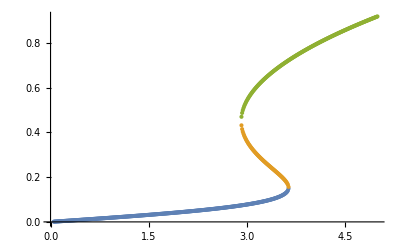

```mathematica
ListPlot[{ее1Down,ее1Middle,ее1Up}]
```

```mathematica
s=0.08
```

0.08

```mathematica
Clear[r1]
```

```mathematica
ee=Table[{r1,NSolve[-ct/r1+s+((-1+√(1+(8 ct)/α))^2 α^2)/(16 (1+1/16 (1+1/p) (-1+√(1+(8 ct)/α))^2 α^2+((-1+√(1+(8 ct)/α))^4 α^4 ω)/(256 p)))==0,ct,Reals]},{r1,0.05,5,0.05}]
```

{{0.05,{{ct→0.00100005}}},{0.1,{{ct→0.0020004}}},{0.15,{{ct→0.00300135}}},{0.2,{{ct→0.0040032}}},{0.25,{{ct→0.00500626}}},{0.3,{{ct→0.00601082}}},{0.35,{{ct→0.0070172}}},{0.4,{{ct→0.00802571}}},{0.45,{{ct→0.00903667}}},{0.5,{{ct→0.0100504}}},{0.55,{{ct→0.0110672}}},{0.6,{{ct→0.0120874}}},{0.65,{{ct→0.0131114}}},{0.7,{{ct→0.0141395}}},{0.75,{{ct→0.015172}}},{0.8,{{ct→0.0162093}}},{0.85,{{ct→0.0172519}}},{0.9,{{ct→0.0183}}},{0.95,{{ct→0.0193541}}},{1.,{{ct→0.0204146}}},{1.05,{{ct→0.0214819}}},{1.1,{{ct→0.0225564}}},{1.15,{{ct→0.0236387}}},{1.2,{{ct→0.0247291}}},{1.25,{{ct→0.0258282}}},{1.3,{{ct→0.0269366}}},{1.35,{{ct→0.0280547}}},{1.4,{{ct→0.0291831}}},{1.45,{{ct→0.0303225}}},{1.5,{{ct→0.0314734}}},{1.55,{{ct→0.0326365}}},{1.6,{{ct→0.0338126}}},{1.65,{{ct→0.0350024}}},{1.7,{{ct→0.0362067}}},{1.75,{{ct→0.0374263}}},{1.8,{{ct→0.0386621}}},{1.85,{{ct→0.0399151}}},{1.9,{{ct→0.0411864}}},{1.95,{{ct→0.0424769}}},{2.,{{ct→0.043788}}},{2.05,{{ct→0.0451209}}},{2.1,{{ct→0.046477}}},{2.15,{{ct→0.0478577}}},{2.2,{{ct→0.0492648}}},{2.25,{{ct→0.0507}}},{2.3,{{ct→0.0521652}}},{2.35,{{ct→0.0536627}}},{2.4,{{ct→0.0551947}}},{2.45,{{ct→0.0567639}}},{2.5,{{ct→0.0583731}}},{2.55,{{ct→0.0600257}}},{2.6,{{ct→0.0617252}}},{2.65,{{ct→0.0634758}}},{2.7,{{ct→0.065282}}},{2.75,{{ct→0.0671493}}},{2.8,{{ct→0.0690836}}},{2.85,{{ct→0.0710922}}},{2.9,{{ct→0.0731831}}},{2.95,{{ct→0.0753662},{ct→0.394781},{ct→0.508154}}},{3.,{{ct→0.0776531},{ct→0.362872},{ct→0.541414}}},{3.05,{{ct→0.0800578},{ct→0.339885},{ct→0.565633}}},{3.1,{{ct→0.0825976},{ct→0.320893},{ct→0.585721}}},{3.15,{{ct→0.085294},{ct→0.304257},{ct→0.603294}}},{3.2,{{ct→0.0881743},{ct→0.289175},{ct→0.619126}}},{3.25,{{ct→0.0912743},{ct→0.275169},{ct→0.633661}}},{3.3,{{ct→0.094642},{ct→0.261909},{ct→0.647178}}},{3.35,{{ct→0.0983445},{ct→0.249135},{ct→0.659871}}},{3.4,{{ct→0.10248},{ct→0.236611},{ct→0.671877}}},{3.45,{{ct→0.107205},{ct→0.224078},{ct→0.683298}}},{3.5,{{ct→0.112789},{ct→0.211185},{ct→0.694216}}},{3.55,{{ct→0.119784},{ct→0.197318},{ct→0.704691}}},{3.6,{{ct→0.129767},{ct→0.180849},{ct→0.714776}}},{3.65,{{ct→0.724511}}},{3.7,{{ct→0.733932}}},{3.75,{{ct→0.743067}}},{3.8,{{ct→0.751942}}},{3.85,{{ct→0.760577}}},{3.9,{{ct→0.768993}}},{3.95,{{ct→0.777204}}},{4.,{{ct→0.785226}}},{4.05,{{ct→0.79307}}},{4.1,{{ct→0.80075}}},{4.15,{{ct→0.808274}}},{4.2,{{ct→0.815652}}},{4.25,{{ct→0.822892}}},{4.3,{{ct→0.830002}}},{4.35,{{ct→0.836988}}},{4.4,{{ct→0.843858}}},{4.45,{{ct→0.850616}}},{4.5,{{ct→0.857268}}},{4.55,{{ct→0.863819}}},{4.6,{{ct→0.870273}}},{4.65,{{ct→0.876635}}},{4.7,{{ct→0.882909}}},{4.75,{{ct→0.889098}}},{4.8,{{ct→0.895205}}},{4.85,{{ct→0.901234}}},{4.9,{{ct→0.907187}}},{4.95,{{ct→0.913069}}},{5.,{{ct→0.91888}}}}

```mathematica
ee1={{0.05,0.004000799549736683},{0.1,0.008006397698032611},{0.15000000000000002,0.01202161318443917},{0.2,0.016051320455638684},{0.25,0.020100487673958365},{0.3,0.024174216414641358},{0.35000000000000003,0.028277783873883345},{0.4,0.032416688501804757},{0.45,0.03659670010479941},{0.5,0.04082391563828379},{0.55,0.04510482214535807},{0.6000000000000001,0.049446368605408464},{0.6500000000000001,0.05385604886156935},{0.7000000000000001,0.058341998328233974},{0.7500000000000001,0.062913107882751},{0.8,0.067579159280039},{0.8500000000000001,0.07235098768182908},{0.9000000000000001,0.0772406785884638},{0.9500000000000001,0.08226180878274371},{1.,0.08742974411164839},{1.05,0.09276201144778635},{1.1,0.09827876860712516},{1.1500000000000001,0.10400340531680233},{1.2000000000000002,0.1099633220581923},{1.2500000000000002,0.11619095424375456},{1.3,0.12272514086152811},{1.35,0.12961298651303318},{1.4000000000000001,0.13691244612645487},{1.4500000000000002,0.14469599516640638},{1.5000000000000002,0.15305597747493438},{1.55,0.16211263136424828},{1.6,0.17202655266722444},{1.6500000000000001,0.18301882556897137},{1.7000000000000002,0.19540505329305835},{1.7500000000000002,0.20965593860566337},{1.8,0.22651122608806132},{1.85,0.2472035861770905},{1.9000000000000001,0.2738820651627212},{1.9500000000000002,0.3100059479604807},{2.,0.3574485513479254},{2.05,0.4074771204912949},{2.1,0.45020080741029134},{2.15,0.4852936541535459},{2.1999999999999997,0.5149154265468638},{2.25,0.5407020431158185},{2.3,0.5637003213230233},{2.35,0.5845881564536209},{2.4,0.6038225408269575},{2.45,0.6217243623078779},{2.5,0.6385271699775926},{2.55,0.6544062162144468},{2.6,0.669496451641232},{2.65,0.6839041008472513},{2.7,0.6977143638213918},{2.75,0.7109966946620182},{2.8,0.72380851588251},{2.85,0.7361978931391814},{2.9,0.7482055012273088},{2.95,0.7598660957265945},{3.,0.7712096326977524},{3.05,0.7822621331581533},{3.1,0.7930463593811294},{3.15,0.8035823503483293},{3.2,0.8138878503280932},{3.25,0.8239786553392022},{3.3,0.833868895797445},{3.35,0.8435712690410234},{3.4,0.8530972321080306},{3.45,0.862457162708556},{3.5,0.8716604945344895},{3.55,0.8807158317030135},{3.6,0.8896310461108844},{3.65,0.8984133606984794},{3.7,0.9070694210229643},{3.75,0.9156053570739435},{3.8,0.924026836899942},{3.85,0.9323391133260088},{3.9,0.9405470648138086},{3.95,0.9486552313324326},{4.,0.9566678459607324},{4.05,0.9645888628225998},{4.1,0.9724219818593978},{4.15,0.9801706708641645},{4.2,0.9878381851367205},{4.25,0.9954275850646714},{4.3,1.0029417518903276},{4.35,1.0103834018860494},{4.4,1.0177550991291},{4.45,1.0250592670406655},{4.5,1.0322981988313773},{4.55,1.0394740669767815},{4.6,1.0465889318301116},{4.65,1.0536447494660164},{4.7,1.0606433788371463},{4.75,1.0675865883154378},{4.8,1.074476061681244},{4.8500000000000005,1.0813134036159753},{4.9,1.0881001447474201},{4.95,1.0948377462912875},{5.,1.1015276043275994}};
```

Now, we reproduce the right panel of Figure 5, plotting ct for s=0.08 (monostable)

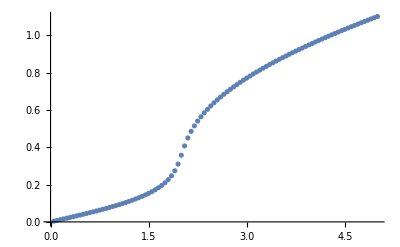

```mathematica
ListPlot[ee1]
```